```mathematica
S1 = {a1 Cos[ϕ1]Sin[θ1], a1 Sin[ϕ1]Sin[θ1],a1 Cos[θ1]}
```

{a1 Cos[ϕ1] Sin[θ1],a1 Sin[θ1] Sin[ϕ1],a1 Cos[θ1]}

```mathematica
S2 = {a2 Cos[ϕ2]Sin[θ2], a2 Sin[ϕ2]Sin[θ2],a2 Cos[θ2]}
```

{a2 Cos[ϕ2] Sin[θ2],a2 Sin[θ2] Sin[ϕ2],a2 Cos[θ2]}

```mathematica
A1 = 2+(3 m2)/(2 m1)
```

2+(3 m2)/(2 m1)

```mathematica
A2 = 2+(3 m1)/(2 m2)
```

2+(3 m1)/(2 m2)

```mathematica
S1perp = m1 m1 √(S1[[1]]*S1[[1]] + S1[[2]]S1[[2]])
```

m1^2 √(a1^2 Cos[ϕ1]^2 Sin[θ1]^2+a1^2 Sin[θ1]^2 Sin[ϕ1]^2)

```mathematica
S2perp = m2 m2 √(S2[[1]]*S2[[1]] + S2[[2]]S2[[2]])
```

m2^2 √(a2^2 Cos[ϕ2]^2 Sin[θ2]^2+a2^2 Sin[θ2]^2 Sin[ϕ2]^2)

```mathematica
chip1 =(A1 S1perp)/ (A1 m1 m1)//Simplify
```

√(a1^2 Sin[θ1]^2)

```mathematica
chip2 =(A2 S2perp)/ (A1 m1 m1)//Simplify
```

(m2 (3 m1+4 m2) √(a2^2 Sin[θ2]^2))/(m1 (4 m1+3 m2))

```mathematica
D[chip1,θ1]//Simplify
```

Cot[θ1] √(a1^2 Sin[θ1]^2)

```mathematica
D[chip2,θ1]//Simplify
```

0

```mathematica
D[chip2,θ2]//Simplify
```

(m2 (3 m1+4 m2) Cot[θ2] √(a2^2 Sin[θ2]^2))/(m1 (4 m1+3 m2))

```mathematica
D[chip1,a1]//Simplify
```

(√(a1^2 Sin[θ1]^2))/a1

```mathematica
D[chip2,a1]//Simplify
```

0

```mathematica
D[chip1,a2]//Simplify
```

0

```mathematica
D[chip2,a2]//Simplify
```

(m2 (3 m1+4 m2) √(a2^2 Sin[θ2]^2))/(a2 m1 (4 m1+3 m2))

```mathematica
D[chip1,m1]//Simplify
```

0

```mathematica
D[chip2,m1]//Simplify
```

-(4 m2 (3 m1^2+8 m1 m2+3 m2^2) √(a2^2 Sin[θ2]^2))/(m1^2 (4 m1+3 m2)^2)

```mathematica
D[chip1,m2]//Simplify
```

0

```mathematica
D[chip2,m2]//Simplify
```

(4 (3 m1^2+8 m1 m2+3 m2^2) √(a2^2 Sin[θ2]^2))/(m1 (4 m1+3 m2)^2)

```mathematica
m1[LNMc_, eta_]:= 1/2(1+ √(1-4*eta))Exp[LNMc]/(eta)^(3/5)
```

```mathematica
m2[LNMc_, eta_]:= 1/2(1- √(1-4*eta))Exp[LNMc]/(eta)^(3/5)
```

```mathematica
Solve[{m1[LNMc,et] == M1, m2[LNMc,et]==M2},{LNMc,et}]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{LNMc→Log[(M1^(3/5) M2^(3/5))/(M1+M2)^(1/5)],et→(M1 M2)/(M1+M2)^2},{LNMc→Log[-((-1)^(1/5) M1^(3/5) M2^(3/5))/(M1+M2)^(1/5)],et→(M1 M2)/(M1+M2)^2},{LNMc→Log[((-1)^(2/5) M1^(3/5) M2^(3/5))/(M1+M2)^(1/5)],et→(M1 M2)/(M1+M2)^2},{LNMc→Log[-((-1)^(3/5) M1^(3/5) M2^(3/5))/(M1+M2)^(1/5)],et→(M1 M2)/(M1+M2)^2},{LNMc→Log[((-1)^(4/5) M1^(3/5) M2^(3/5))/(M1+M2)^(1/5)],et→(M1 M2)/(M1+M2)^2}}

```mathematica
jac =Det[{{D[m1[Mc,eta],Mc],D[m1[Mc,eta],eta]},{D[m2[Mc,eta],Mc] ,D[m2[Mc,eta],eta]}}]/.Mc->Log[Mc]//FullSimplify
```

Mc^2/(√(1-4 eta) eta^(6/5))

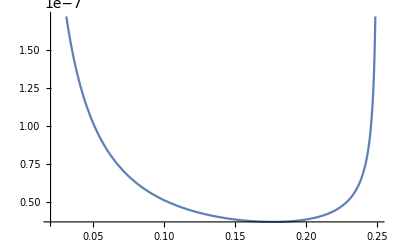

```mathematica
Plot[jac/.Mc->10*5*^-6,{eta, 1/50,.25}]
```

```mathematica
m1qMc[LNMc_,q_]:= LNMc/(1+q)(q/(1+q)^2)^(-3/5)
m2qMc[LNMc_,q_]:= LNMc/(1+q)q(q/(1+q)^2)^(-3/5)
```

```mathematica
jac = Det[{{D[m1qMc[LMc,q],LMc], D[m1qMc[LMc,q],q]},{D[m2qMc[LMc,q],q],D[m2qMc[LMc,q],LMc]}}]//Simplify
```

-m1qMc^(0,1)[LMc,q] m2qMc^(0,1)[LMc,q]+m1qMc^(1,0)[LMc,q] m2qMc^(1,0)[LMc,q]

```mathematica
m1qMc[Mc,q]/.Mc->(Subscript[m, 1] Subscript[m, 2])^(3/5)/(Subscript[m, 1]+Subscript[m, 2])^(1/5)/.q->Subscript[m, 2]/Subscript[m, 1]//Expand//FullSimplify
```

(m_1 ((m_1 m_2)/(m_1+m_2)^2)^(2/5) (m_1+m_2)^(4/5))/(m_1 m_2)^(2/5)

```mathematica
Mc/m1qMc[Mc,q]^2//FullSimplify
```

(q (q/(1+q)^2)^(1/5))/Mc

```mathematica
1/(jac/Mc)-(q (q/(1+q)^2)^(1/5))/Mc/.LMc->Log[Mc]//Simplify
```

0

```mathematica
CForm[jac]
```

Power(E,2*Mc)/(Sqrt(1 - 4*eta)*Power(eta,1.2))

```mathematica
1/D[Log[m],m]
```

m

```mathematica
chirpm[m1_,m2_]:= (m1 m2)^(3/5)/(m1+m2)^(1/5)
```

```mathematica
eta[m1_,m2_]:= (m1 m2)/(m1+m2)^2
```

```mathematica
eta[12,1]
```

12/169

```mathematica
Solve[{chirpm[m1,m2]==Mc, eta[m1,m2]==et},{m1,m2}]//FullSimplify
```

{{m1→-(-1/2)^(1/5) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5),m2→((-1/2)^(1/5) ((-1+2 et) (1+(-3+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/(2 et (1+(-3+et) et) Mc^5)},{m1→((((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→((((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5) ((1+et (-5+(7-2 et) et)) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)},{m1→((-1)^(2/5) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→((-1)^(2/5) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5) ((1+et (-5+(7-2 et) et)) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)},{m1→-((-1)^(3/5) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→((-1)^(3/5) ((-1+2 et) (1+(-3+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)},{m1→((-1)^(4/5) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→((-1)^(4/5) (((1+5 (-1+et) et) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5) ((1+et (-5+(7-2 et) et)) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)},{m1→-(-1/2)^(1/5) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5),m2→((-1/2)^(1/5) ((-1+2 et) (1+(-3+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/(2 et (1+(-3+et) et) Mc^5)},{m1→((((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→(((1+et (-5+(7-2 et) et)) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)},{m1→((-1)^(2/5) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→((-1)^(2/5) ((1+et (-5+(7-2 et) et)) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)},{m1→-((-1)^(3/5) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→((-1)^(3/5) ((-1+2 et) (1+(-3+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)},{m1→((-1)^(4/5) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/2^(1/5),m2→((-1)^(4/5) ((1+et (-5+(7-2 et) et)) Mc^5-√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10)) (((1+5 (-1+et) et) Mc^5+√(-(-1+4 et) (1+(-3+et) et)^2 Mc^10))/et^3)^(1/5))/(2 2^(1/5) et (1+(-3+et) et) Mc^5)}}

```mathematica
Log[D[Exp[LnDl]^3,LnDl]]//Simplify
```

Log[3 ⅇ^(3 LnDl)]

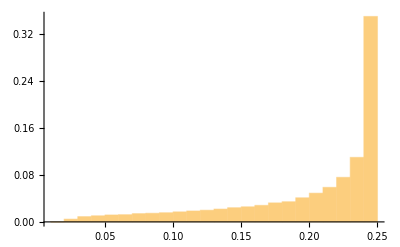

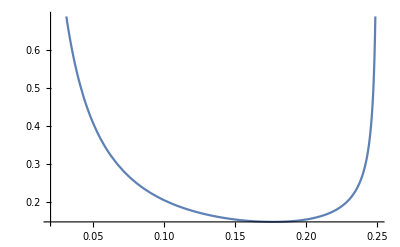

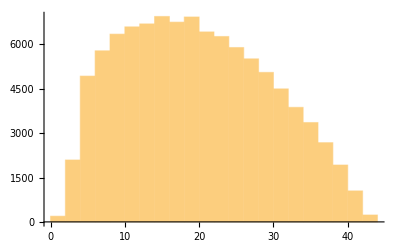

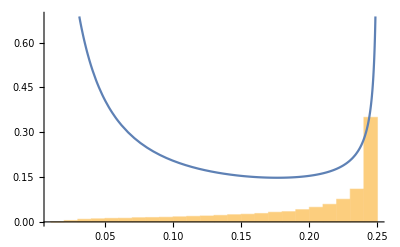

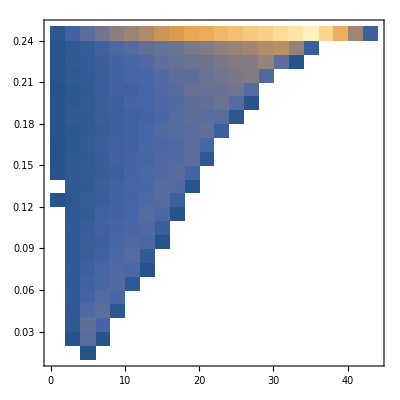

```mathematica
M1vec = Table[RandomReal[{1,50}],{x,0,100000}];
M2vec = Table[RandomReal[{1,50}],{x,0,Length[M1vec]}];
etavec = Table[ M1vec[[i]]*M2vec[[i]]/ ( M1vec[[i]]+M2vec[[i]])^2,{i,1,Length[M1vec]}];
Mcvec = Table[ (M1vec[[i]]*M2vec[[i]])^(3/5)/ ( M1vec[[i]]+M2vec[[i]])^(1/5),{i,1,Length[M1vec]}];
etaMc = Table[ { Mcvec[[i]],etavec[[i]]},{i,1,Length[Mcvec]}];
H1 = Histogram[etavec,Automatic,"Probability"]
P1 = Plot[jac/.Mc->.1,{eta, 1/50,.25}]
Histogram[Mcvec]
Show[{H1,P1}]
DensityHistogram[etaMc,Automatic, "Probability"]
```